```mathematica
g=9.81;
mp=0.1;
mc=1;
l=0.5;
F=0;
```

```mathematica
sol=NDSolveValue[{
θ''[t]==(g*Sin[θ[t]]+Cos[θ[t]]*(-F-mp*l*θ'[t]^2*Sin[θ[t]])/(mc+mp))/(l*(4/3-(mp*Cos[θ[t]]^2)/(mc+mp))),
x''[t]==(F+mp*l*(θ'[t]^2*Sin[θ[t]]-θ''[t]*Cos[θ[t]]))/(mc+mp),
x[0]==-0.01258566,
x'[0]==-0.00156614,
θ[0]==0.04207708,
θ'[0]==-0.00180545
},{x[t],x'[t],θ[t],θ'[t]},{t,0,6}];
```

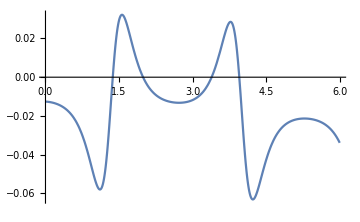
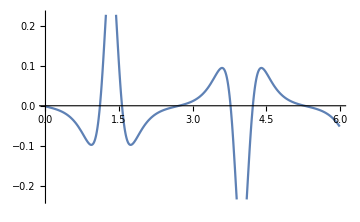
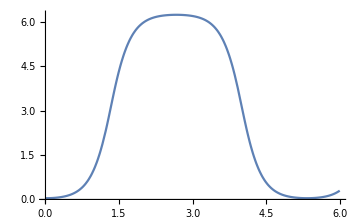
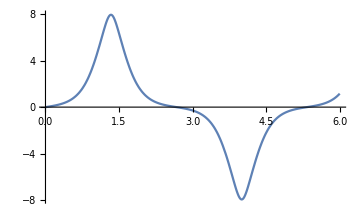

```mathematica
Row[{
Plot[sol[[1]]/.{t->t},{t,0,6},ImageSize->Medium],
Plot[sol[[2]]/.{t->t},{t,0,6},ImageSize->Medium],
Plot[sol[[3]]/.{t->t},{t,0,6},ImageSize->Medium],
Plot[sol[[4]]/.{t->t},{t,0,6},ImageSize->Medium]
}]
```